```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sandrews/SSA/software/Smoldyn/trunk/examples/S4_molecules/fluctuations

```mathematica
simdata=Import["fluctuationsout.txt"];
```

```mathematica
simdata2=StringReplace[simdata," "->","];
```

```mathematica
simdata3=ImportString[simdata2,"CSV"];
```

```mathematica
timedata=simdata3[[All,1]];
```

```mathematica
leftdata=simdata3[[All,2]];
```

```mathematica
rightdata=simdata3[[All,3]];
```

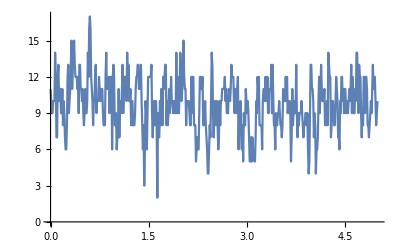

```mathematica
ListLinePlot[Transpose[{timedata[[1;;500]],leftdata[[1;;500]]}]]
```

```mathematica
leftaverage=N[Mean[leftdata]]
```

10.0112

```mathematica
rightaverage=N[Mean[rightdata]]
```

9.9888

```mathematica
leftprob=leftaverage/(leftaverage+rightaverage)
```

0.50056

```mathematica
rightprob=rightaverage/(leftaverage+rightaverage)
```

0.49944

```mathematica
leftvariance=N[Variance[leftdata]]
```

4.99007

```mathematica
rightvariance=N[Variance[rightdata]]
```

4.99007

```mathematica
(* binomial distribution variance is np(1-p)
The following number variable is the computed total number of particles *)
number=leftvariance/(leftprob*rightprob)
```

19.9603

```mathematica
leftcorrelation=N[CorrelationFunction[leftdata,{10}]];
```

```mathematica
timeforcorrelation=timedata[[1;;11]];
```

```mathematica
corrdata=Transpose[{timeforcorrelation,leftcorrelation}]
```

{{0,1.},{0.01,0.500027},{0.02,0.313116},{0.03,0.206103},{0.04,0.121454},{0.05,0.0707135},{0.06,0.0399914},{0.07,0.0353016},{0.08,0.0211945},{0.09,0.0164248},{0.1,0.00742627}}

```mathematica
model=a*Exp[-k*t];
```

```mathematica
fit=FindFit[corrdata,model,{a,k},t]
```

{a→0.976847,k→56.5781}

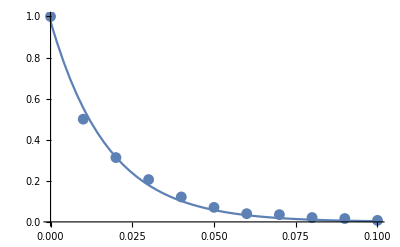

```mathematica
Show[{ListPlot[corrdata,PlotRange->All],Plot[model/.fit,{t,0,0.1},PlotRange->All]}]
```

```mathematica
(* I was expecting that this rate constant would relate to diffusion coefficient as k = 2*D/l^2 where D is the diffusion coefficient and l is half of the cell length.  However it actually seems to agree with k = 3*D/l^2. *)
```

```mathematica
halflength=1
```

1

```mathematica
diffconst=(k/.fit)*halflength^2/3
```

18.8594